# ModeCode Engine

## Multifield Background and Perturbation Solver

## Define Potential and Derivatives

### Main Functions

```mathematica
d=2;
ϕ=Map[Symbol["ϕ"<>ToString[#]][α]&,Range[d]];
dϕ=Map[Symbol["dϕ"<>ToString[#]][α]&,Range[d]];
ψ=Table[Symbol["ψ"<>ToString[i]<>ToString[j]][α],{i,d},{j,d}];
dψ=Table[Symbol["dψ"<>ToString[i]<>ToString[j]][α],{i,d},{j,d}];

ϕfunct=Map[Symbol["ϕ"<>ToString[#]]&,Range[d]];
dϕfunct=Map[Symbol["dϕ"<>ToString[#]]&,Range[d]];
ψfunct=Table[Symbol["ψ"<>ToString[i]<>ToString[j]],{i,d},{j,d}];
dψfunct=Table[Symbol["dψ"<>ToString[i]<>ToString[j]],{i,d},{j,d}];
```

### Model Definition

```mathematica
m2=10^{-10.422895047377294,-10.422895047377294+Log10[81.0]};
(*m2=10^{-10.965,-10.0106};*)

V:=(1./2)m2.(ϕ*ϕ) (*Scalar*)
(*dVdϕ:=m2*ϕ  (*Vector*)
m2matrix:={{m2[[1]],0},{0,m2[[2]]}} (*Hessian matrix for V, ddV/dϕ_idϕ_j*)*)

(*Λ=6.8*^-6;
M=.03;
μ=500;
ν=.015;

V:=Λ^4((1-ϕ[[2]]^2/M^2)^2+ϕ[[1]]^2/μ^2+(ϕ[[1]]^2 ϕ[[2]]^2)/ν^4)*)
(*V:=(1./2)m2.(ϕ*ϕ)*)
dVdϕ:=Table[D[V,ϕ[[i]]],{i,1,d}]
m2matrix:=Table[D[D[V,ϕ[[i]]],ϕ[[j]]],{i,1,d},{j,1,d}]
```

## Cosmology Functions --- scalars

### General

```mathematica
ϵ:=1/2 dϕ.dϕ (*Also = KE/H^2*)
H:=Sqrt[V/(3.-ϵ)](*G=Subscript[M, P]^2/8π*)
H2:=V/(3.-ϵ)

KE:=H2 ϵ

weqnstate:=2/3 ϵ-1.
```

### Slow Roll

```mathematica
ϵSR:=1/(2 V^2)dVdϕ.dVdϕ
HSR:=Sqrt[V/3.]
H2SR:=V/3
```

## Set Parameters and Initial Conditions

```mathematica
ϕ0={10.31001,12.93651};
ϕ0={0.31001,22.93651};
(*ϕ0={0.2864586827*^02,0.2069510045*^02};*)

(*ϕ0={13,13};*)
(*ϕcrit=Sqrt[2] ν^2/M
ϕ0={ϕcrit,0}*)
dϕ0=-dVdϕ/(3 H2SR)/.Thread[ϕ->ϕ0];(*slow roll w/negligble KE contrib*)

(*Set other*)
a0=1.;
Npivot=55;

a:=a0 Exp[α]

Mpc2Mpl=2.6245*^-57;
kpivot=.002 Mpc2Mpl;(*Specify in Mpc and converts to Subscript[M, Pl]^-1*)
```

## Background Solver

Evolve background until end of inflation

### Background Equations

```mathematica
kgeqn=Flatten[
Map[Thread,
{D[dϕ,α]+(3-ϵ)dϕ+(1/H2)dVdϕ==0,
 dϕ==D[ϕ,α],
ϕ==ϕ0/.α->0,
dϕ==dϕ0/.α->0}
]];
```

### Engine

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
αend=1000000;
background=NDSolve[kgeqn,Flatten[{ϕfunct,dϕfunct}],{α,0,αend},Method ->{"EventLocator","Event"->{ϵ-1.}},Method->"BDF"]
αend = InterpolatingFunctionDomain[First[ϕ1/.background]][[1,2]]
αexit=αend-Npivot
```

{{ϕ1→InterpolatingFunction[{{0.,132.203}},<>],ϕ2→InterpolatingFunction[{{0.,132.203}},<>],dϕ1→InterpolatingFunction[{{0.,132.203}},<>],dϕ2→InterpolatingFunction[{{0.,132.203}},<>]}}

132.203

77.2034

### Renormalize a by a_*H_*=k_* and get horizon crossing values and α to start ptb equations at

```mathematica
Hpivot=(H/.background/.α->αexit)[[1]];


a0=kpivot/(Hpivot Exp[αexit]) (*kpivot already in Subscript[M, Pl]^-1*);
FindRoot[{a H-kpivot/100}/.background,{α,αexit}];
αptbstart=α/.%;

a0=a/.α->αptbstart;
```

## Perturbation Equations

### NOTE: Now time translate background values by time when perturbation equations needs to start αptbstart. Everything from here down is in “perturbation time.”

### ICs for perturbation mode matrix ψ_IJ in Bunch-Davies vacuum (See Salopek, Bond, Bardeen) based on background values when a_*H_*=k_*/100

```mathematica
ϕptbstart=Flatten[ϕ/.background/.α->αptbstart];
dϕptbstart=Flatten[dϕ/.background/.α->αptbstart];
Hptbstart=(H/.background/.α->αptbstart)[[1]];
ψ0[k_]:=(1/Sqrt[2k])IdentityMatrix[d]
dψ0[k_]:=(-I/(a Hptbstart) )Sqrt[k/2] IdentityMatrix[d]/.α->0

(*Q-variable*)
(*ψ0[k_]:=((a/Sqrt[2k])IdentityMatrix[d])/.α->0
dψ0[k_]:=((-I/(a^2 Hptbstart) )Sqrt[k/2] IdentityMatrix[d] - (a/Sqrt[2k])IdentityMatrix[d])/.α->0*)
```

### Functions for ptbs

```mathematica
ptbmassmatrix=Table[(1./H2)(m2matrix[[i,j]]+dϕ[[i]]dVdϕ[[j]]+dVdϕ[[i]]dϕ[[j]])+(3.-ϵ)dϕ[[i]]dϕ[[j]],{i,d},{j,d}];
```

### Perturbed, Fourier-transformed Equations

```mathematica
ptbeqn=Flatten[
{Table[D[dψ[[i,j]],α]==-(1-ϵ)dψ[[i,j]]-((kpivot/(a H))^2-2+ϵ)ψ[[i,j]]-Sum[ptbmassmatrix[[i,l]]ψ[[l,j]],{l,d}],{i,1,d},{j,1,d}],
Table[D[ψ[[i,j]],α]==dψ[[i,j]],{i,1,d},{j,1,d}],
Table[ψ[[i,j]]==ψ0[kpivot][[i,j]]/.α->0,{i,1,d},{j,1,d}],
Table[dψ[[i,j]]==dψ0[kpivot][[i,j]]/.α->0,{i,1,d},{j,1,d}]}
];

(*Q-variable*)
(*ptbeqn=Flatten[
{Table[D[dψ[[i,j]],α]==-(3-ϵ)dψ[[i,j]]-((kpivot/(a H))^2)ψ[[i,j]]-Sum[ptbmassmatrix[[i,l]]ψ[[l,j]],{l,d}],{i,1,d},{j,1,d}],
Table[D[ψ[[i,j]],α]==dψ[[i,j]],{i,1,d},{j,1,d}],
Table[ψ[[i,j]]==ψ0[kpivot][[i,j]]/.α->0,{i,1,d},{j,1,d}],
Table[dψ[[i,j]]==dψ0[kpivot][[i,j]]/.α->0,{i,1,d},{j,1,d}]}
];*)


backeqn=Flatten[
Map[Thread,
{D[dϕ,α]+(3-ϵ)dϕ+(1/H2)dVdϕ==0,
 dϕ==D[ϕ,α],
ϕ==ϕptbstart/.α->0,
dϕ==dϕptbstart/.α->0}
]];
fulleqn=Join[ptbeqn,backeqn];
```

## Perturbation Solver

Evolve the background again, too?

```mathematica
αptbend=αend-αptbstart;
perturbations=NDSolve[fulleqn,Flatten[{ϕfunct,dϕfunct,ψfunct,dψfunct}],{α,0,αptbend},Method->"ExplicitRungeKutta",AccuracyGoal->20,MaxSteps->Infinity]
```

{{ϕ1→InterpolatingFunction[{{0.,59.6459}},<>],ϕ2→InterpolatingFunction[{{0.,59.6459}},<>],dϕ1→InterpolatingFunction[{{0.,59.6459}},<>],dϕ2→InterpolatingFunction[{{0.,59.6459}},<>],ψ11→InterpolatingFunction[{{0.,59.6459}},<>],ψ12→InterpolatingFunction[{{0.,59.6459}},<>],ψ21→InterpolatingFunction[{{0.,59.6459}},<>],ψ22→InterpolatingFunction[{{0.,59.6459}},<>],dψ11→InterpolatingFunction[{{0.,59.6459}},<>],dψ12→InterpolatingFunction[{{0.,59.6459}},<>],dψ21→InterpolatingFunction[{{0.,59.6459}},<>],dψ22→InterpolatingFunction[{{0.,59.6459}},<>]}}

```mathematica
Plot[{Re[ψ/.perturbations],Im[ψ/.perturbations]},{α,0,αptbend}]
```

-Graphics-

## Power Spectrum

### Slow-Roll Approximation for Power Spectrum

```mathematica
PowerSpectrumHorizonCross=Flatten[
V/(24 π^2){1/ϵSR,1/ϵ}/.perturbations/.α->αexit-αptbstart]
PowerSpectrumSR=Flatten[
Npivot/(4 π^2) {H2SR,H2}/.perturbations/.α->αexit-αptbstart]
```

{1.53235×10^-7+0. ⅈ,1.54169×10^-7+0. ⅈ}

{1.54743×10^-7+0. ⅈ,1.55215×10^-7+0. ⅈ}

### Numerical Evaluation

```mathematica
PowerSpectrum:=Table[kpivot^3/(2 π^2 a^2)Sum[ψ[[i,l]] Conjugate[ψ][[j,l]],{l,d}],{i,1,d},{j,1,d}]

dϕ0:=Sqrt[dϕ.dϕ]
ω:=dϕ/dϕ0
PowerSpectrumAdiabatic:=(1.0/(2.0ϵ))Sum[ω[[i]] ω[[j]] PowerSpectrum[[i,j]],{i,1,d},{j,1,d}]



Print["Numerical -- Inflation End: ",PowerSpectrumAdiabatic/.perturbations/.α->αptbend,
"\nNumerical -- Horiz Cross: ", PowerSpectrumAdiabatic/.perturbations/.α->αexit-αptbstart,
 "\nSlowroll: ",PowerSpectrumSR[[1]],
 "\nHorizon Crossing: ",PowerSpectrumHorizonCross[[1]]]
```

Numerical -- Inflation End: {1.5597×10^-7+0. ⅈ}
Numerical -- Horiz Cross: {3.13325×10^-7+0. ⅈ}
Slowroll: 1.54743×10^-7+0. ⅈ
Horizon Crossing: 1.53235×10^-7+0. ⅈ

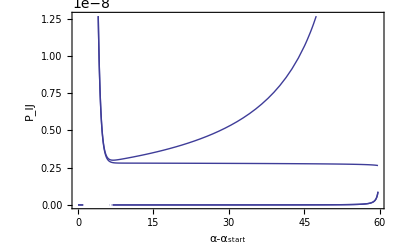

Graphics::gprim: ThickRed was encountered where a Graphics primitive or directive was expected.

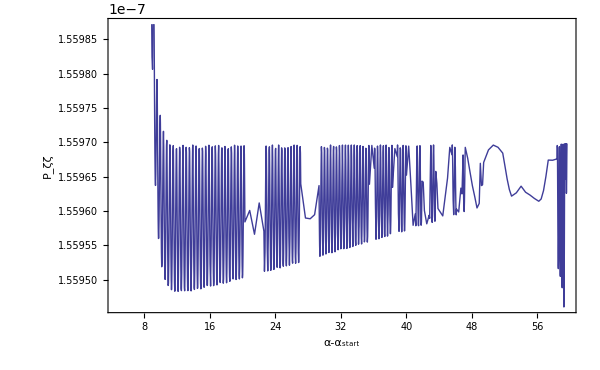

```mathematica
Plot[PowerSpectrum/.perturbations,{α,0,αptbend},Frame->True,FrameLabel->Map[Style[#,20]&,{α-Subscript[α, start],Subscript[P, IJ]}]]
laynepk=Plot[PowerSpectrumAdiabatic/.perturbations,{α,αexit-αptbstart,αptbend},GridLines->{{αexit},{}},
Frame->True,FrameLabel->Map[Style[#,20]&,{α-Subscript[α, start],Subscript[P, ζζ]}],PlotStyle->{ThickRed}]
```

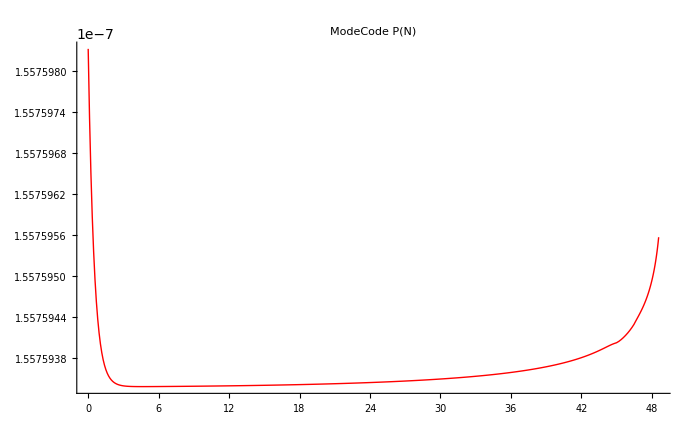

```mathematica
SetDirectory["/home/lpri691/Cosmology_Research/F_projects/ModeCode/ModeCode_multifield"];
realpz = Import["fort.2","Table"];
realpz[[All,1]]=realpz[[All,1]]-realpz[[1,1]];
modepk=ListPlot[realpz[[1;;All,{1,2}]],Joined->True,PlotRange->All,PlotLabel->"ModeCode P(N)",PlotStyle->Red]
```

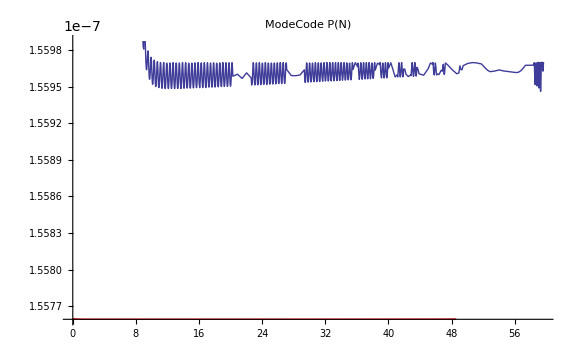

```mathematica
Show[modepk,laynepk]
```

```mathematica
(*Export["agreement.pdf",Show[laynepk,jonnyplot]]*)
```

## Other Plots

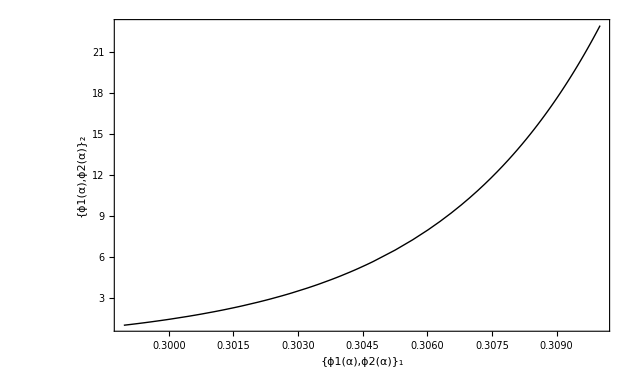

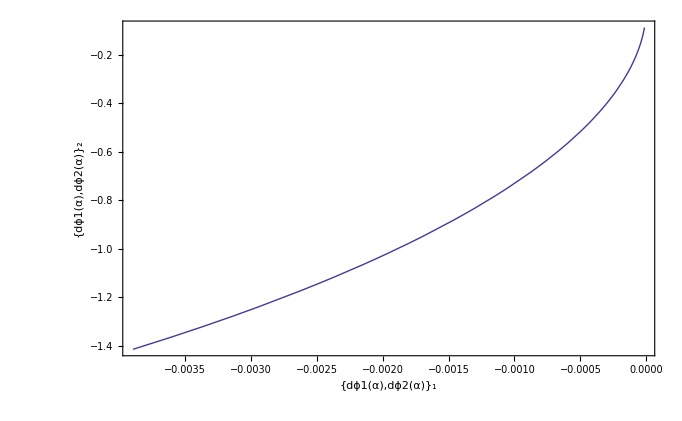

```mathematica
plotfrommathematica=Show[ParametricPlot[ϕ/.background,{α,0,αend},Frame->True,PlotStyle->{Black,Thick},PlotRange->All,FrameLabel->Map[Style[#,20]&,{Subscript[ϕ, 1],Subscript[ϕ, 2]}]],ListPlot[{ϕ[0]}/.background,PlotMarkers->{Automatic,Medium},PlotStyle->Black,Frame->True],AspectRatio->1/GoldenRatio]
Show[ParametricPlot[dϕ/.background,{α,0,αend},PlotStyle->{Thick},PlotRange->All,Frame->True,FrameLabel->{Style[Subscript[dϕ, 1],20],Style[Subscript[dϕ, 2],20]},AspectRatio->1/GoldenRatio],ListPlot[{dϕ[0]}/.background,PlotMarkers->{Automatic,Medium},PlotStyle->Black,Frame->True]]
```

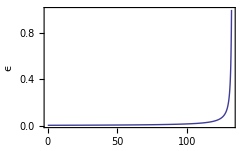

```mathematica
Plot[ϵ/.background,{α,0,αend},PlotRange->All,Frame->True,FrameLabel->{Style[α,20],Style["ϵ",20]}]
```

```mathematica
SetDirectory["/home/lpri691/Cosmology_Research/F_projects/ModeCode/ModeCode_multifield"];
data=Import["fort.1","Table"];
dataα=data[[All,1]];
dataϕ1=data[[All,2]];
dataϕ2=data[[All,3]];
plotfrommodecode=ListPlot[Thread[{dataϕ1,dataϕ2}],Joined->True,PlotRange->All]
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-

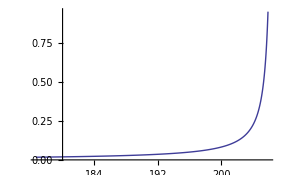

```mathematica
ListPlot[data[[500;;All,{1,6}]],Joined->True,PlotRange->All]
```

```mathematica
compare=Show[plotfrommathematica,plotfrommodecode,AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*ModeCode Comparison*)
SetDirectory["/home/lpri691/Cosmology_Research/F_projects/ModeCode/ModeCode_multifield"];
```

```mathematica
Labels=Directive[Darker[Blue],FontFamily->"Helvetica Neue",FontSize->12];
ThickBlue=Directive[Thick,Blue];
ThickRed=Directive[Thick,Red];
ThickOrange=Directive[Thick,Orange];
ThickGreen=Directive[Thick,Green];
ThickPurple=Directive[Thick,Purple];
ThickYellow=Directive[Thick,Darker[Yellow,0.2]];
ThickDarkRed=Directive[Thick,Blend[{Red,Blue},0.15]];
```

```mathematica
realdata=Import["fort.20","Table"];
realdata[[All,1]]=realdata[[All,1]]-realdata[[1,1]];
```

```mathematica
mathdata=realdata;
mathdata[[All,2]]=Flatten[Re[ψ[[1,1]]]/.perturbations/.α->#&@realdata[[All,1]]]-realdata[[All,2]];
mathdata[[All,2]]=mathdata[[All,2]]/realdata[[All,2]];
```

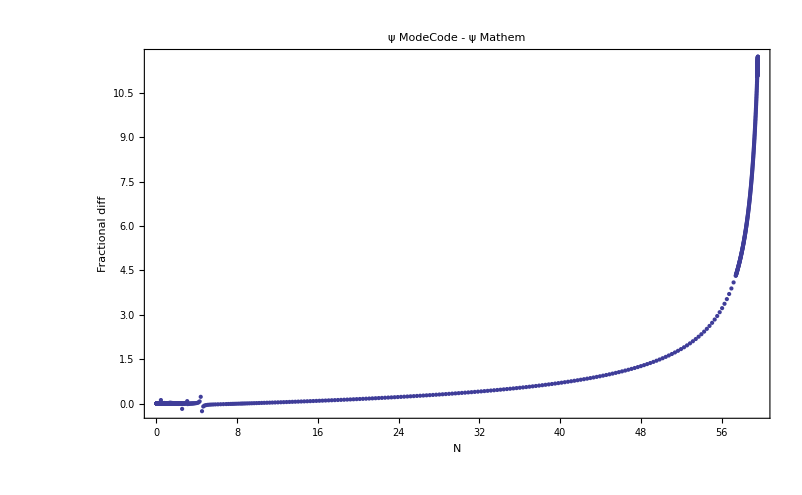

```mathematica
ListPlot[mathdata[[All,1;;2]],PlotRange->All,PlotLabel->"ψ ModeCode - ψ Mathem",Frame->True,FrameLabel->{N,"Fractional diff"}]
```

```mathematica
modecodeplot=ListPlot[realdata[[All,{1,2}]],Joined->True,PlotRange->All]
mathematicaplot=Plot[{Re[ψ[[1,1]]/.perturbations]},{α,0,αptbend},PlotRange->All,PlotStyle->ThickDarkRed,PlotLabel->"ψ_11 Adiabatic"]
Show[mathematicaplot,modecodeplot]
```

-Graphics-

-Graphics-

-Graphics-